```mathematica
(** Problem 2: defining functions **) 
(* Basic mathematica file to produce tensor products of sigma matrices *)

identity := {{1, 0}, {0, 1}}
sigma[1] := {{0, 1}, {1, 0}}/2
sigma[2] := {{0, -I}, {I, 0}}/2
sigma[3] := {{1, 0}, {0, -1}}/2

(* tensor product of a pair of matrices *)

tensor[m1_, m2_] :=
  With[{l1 = Length[m1], l2 = Length[m2]},
    Table[m1[[Quotient[i - 1, l2] + 1, Quotient[j - 1, l2] + 1]] *
            m2[[Mod[i -1, l2] + 1, Mod[j -1, l2] + 1]], 
          {i, 1, l1 l2}, {j, 1, l1 l2}]]

(* takes the tensor product of an arbitrary number of matrices *)

tensor[m1_, m2_, rest___] :=
  Apply[tensor, {tensor[m1, m2], rest}]

(* gets the matrix i for any number n *)

list[n_, i_, r_] := 
   RotateLeft[Join[Table[identity, {n-2}], {sigma[i], sigma[i]}], r]

ii[n_] :=Sum[Apply[tensor, list[n, i, r]],{ i, 1, 3},{r, 1, n}]

(* gets the matrix S_z for any n *)

list2[n_, r_] := 
   RotateLeft[Join[Table[identity, {n-1}], {sigma[3]}], r]

sz[n_] :=Sum[Apply[tensor, list2[n, r]], {r, 1, n}]

(* the matrix H from problem 5g *)

h[n_, x_] := x sz[n] -(1-x) ii[n]

v[n_, x_, i_] := Sort[Eigensystem[h[n, x]][[1]]][[i]]
v[n_, x_] := Sort[Eigensystem[h[n, x]][[1]]]

plot1[n_, i_] := Plot[v[n, x, i],{x, 0, 1},PlotRange-> All]
plotn[n_] := Apply[Show,Table[plot1[n, i],{ i, 1, 2^n}]]
```

```mathematica
(** Problem 2(d) **)
```

```mathematica
Eigensystem[ii[2]]
```

{{-3/2,1/2,1/2,1/2},{{0,-1,1,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}}}

```mathematica
Eigensystem[ii[3]]
```

{{-3/4,-3/4,-3/4,-3/4,3/4,3/4,3/4,3/4},{{0,0,0,-1,0,0,1,0},{0,0,0,-1,0,1,0,0},{0,-1,0,0,1,0,0,0},{0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,1,1,0},{0,1,1,0,1,0,0,0},{1,0,0,0,0,0,0,0}}}

```mathematica
Eigensystem[ii[4]]
```

{{-2,-1,-1,-1,1,1,1,1,1,0,0,0,0,0,0,0},{{0,0,0,1,0,-2,1,0,0,1,-2,0,1,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,1,0,-1,1,0},{0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0},{0,-1,1,0,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,1,0,1,1,0},{0,0,0,1,0,1,1,0,0,1,1,0,1,0,0,0},{0,1,1,0,1,0,0,0,1,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
(** Problem 2 (g) **)
```

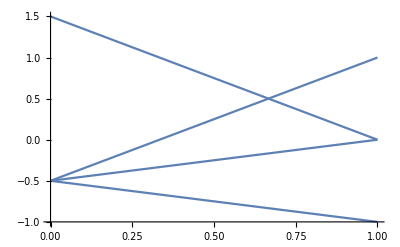

```mathematica
plotn[2]
```

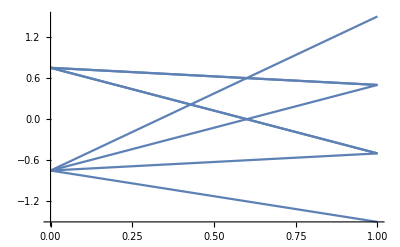

```mathematica
plotn[3]
```

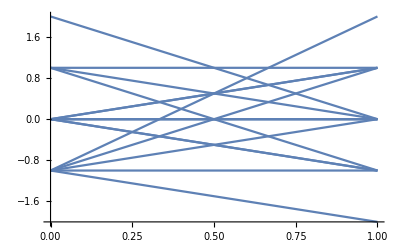

```mathematica
plotn[4]
```

```mathematica
(** Problem 3 **)
```

```mathematica
(** We explicitly find the probabilities for one series of outcomes in problem 3(c) as an example; problem 3(b) is a simpler case and the generalization to (d) is direct **)
```

```mathematica
(** One-site measurement operators for hbar/2 or -hbar/2 **) 
Projup = {{1,0},{0,0}};
Projdown= {{0,0},{0,1}};
(** One-site measurement operators for hbar^2/4 or -3hbar^2/4 **) 
Proja =KroneckerProduct[{1,0,0,0},{1,0,0,0}]+ KroneckerProduct[{0,0,0,1},{0,0,0,1}] +KroneckerProduct[{0,1/√2,1/√2,0},{0,1/√2,1/√2,0}]
Projb= KroneckerProduct[{0,1/√2,-1/√2,0},{0,1/√2,-1/√2,0}]
(** measurement operators on full system for measuring S_z^2 **) 
Projup2= KroneckerProduct[{{1,0},{0,1}}, Projup, {{1,0},{0,1}},{{1,0},{0,1}}];
Projdown2= KroneckerProduct[{{1,0},{0,1}}, Projdown, {{1,0},{0,1}},{{1,0},{0,1}}];
```

{{1,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,1}}

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
(** measurement operators on full system for measuring S_2.S_3 **)
```

```mathematica
Proja23 = KroneckerProduct[{{1,0},{0,1}},Proja, {{1,0},{0,1}}]; 
Projb23=KroneckerProduct[{{1,0},{0,1}},Projb, {{1,0},{0,1}}];
```

```mathematica
(** measurement operators on full system for measuring S_3.S_4 **)
```

```mathematica
Proja34 = KroneckerProduct[{{1,0},{0,1}},{{1,0},{0,1}},Proja]; 
Projb34=KroneckerProduct[{{1,0},{0,1}}, {{1,0},{0,1}},Projb];
```

```mathematica
(** Density matrix of initial state **)
```

```mathematica
Initial =Flatten[KroneckerProduct[{1,1}/√2,{1,1}/√2,{1,1}/√2,{1,1}/√2]];
```

```mathematica
(** Functions for evaluating final states and probabilities corresponding to initial state psi and measurement operator M **)
```

```mathematica
Prob[psi_, M_]:= Conjugate[psi].(M.psi)
Final[psi_,M_]:=M.psi/(Conjugate[psi].(M.psi))^(1/2)
```

```mathematica
(** Probability of outcome hbar/2 --> hbar^2/4 --> hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projup2]
```

1/2

```mathematica
rhoup = Final[Initial, Projup2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Proja23]
```

3/4

```mathematica
rhof1 =Final[rhoup,Proja23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Proja34]
```

11/12

```mathematica
(** So the overall probability of this series of outcomes is 1/2*3/4*11/12 = 11/32. **)
```

```mathematica
(** Probability of outcome hbar/2 --> hbar^2/4 --> -3 hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projup2]
```

1/2

```mathematica
rhoup = Final[Initial, Projup2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Proja23]
```

3/4

```mathematica
rhof1 =Final[rhoup,Proja23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Projb34]
```

1/12

```mathematica
(** So the overall probability of this series of outcomes is 1/2*3/4*1/12 = 1/32.  **)
```

```mathematica
(** Probability of outcome hbar/2 --> -3 hbar^2/4 --> hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projup2]
```

1/2

```mathematica
rhoup = Final[Initial, Projup2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Projb23]
```

1/4

```mathematica
rhof1 =Final[rhoup,Projb23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Proja34]
```

3/4

```mathematica
(** So the overall probability of this series of outcomes is 1/2*1/4*3/4 = 3/32.  **)
```

```mathematica
(** Probability of outcome hbar/2 --> -3 hbar^2/4 --> -3 hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projup2]
```

1/2

```mathematica
rhoup = Final[Initial, Projup2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Projb23]
```

1/4

```mathematica
rhof1 =Final[rhoup,Projb23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Projb34]
```

1/4

```mathematica
(** So the overall probability of this series of outcomes is 1/2*1/4*1/4 = 1/32.  **)
```

```mathematica
(** Probability of outcome -hbar/2 -->  hbar^2/4 -->  hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projdown2]
```

1/2

```mathematica
rhoup = Final[Initial, Projdown2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Proja23]
```

3/4

```mathematica
rhof1 =Final[rhoup,Proja23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Proja34]
```

11/12

```mathematica
(** So the overall probability of this series of outcomes is 1/2*3/4*11/12 = 11/32.  **)
```

```mathematica
(** Probability of outcome -hbar/2 -->  hbar^2/4 -->  -3 hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projdown2]
```

1/2

```mathematica
rhoup = Final[Initial, Projdown2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Proja23]
```

3/4

```mathematica
rhof1 =Final[rhoup,Proja23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Projb34]
```

1/12

```mathematica
(** So the overall probability of this series of outcomes is 1/2*3/4*1/12 = 1/32.  **)
```

```mathematica
(** Probability of outcome -hbar/2 -->  -3 hbar^2/4 -->   hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projdown2]
```

1/2

```mathematica
rhoup = Final[Initial, Projdown2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Projb23]
```

1/4

```mathematica
rhof1 =Final[rhoup,Projb23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Proja34]
```

3/4

```mathematica
(** So the overall probability of this series of outcomes is 1/2*1/4*3/4 = 3/32.  **)
```

```mathematica
(** Probability of outcome -hbar/2 -->  -3 hbar^2/4 -->  -3 hbar^2/4 **)
```

```mathematica
(** First step: measure S2 **)
```

```mathematica
p1= Prob[Initial,Projdown2]
```

1/2

```mathematica
rhoup = Final[Initial, Projdown2];
```

```mathematica
(** second step: measure S2.S3 **)
```

```mathematica
Prob[rhoup,Projb23]
```

1/4

```mathematica
rhof1 =Final[rhoup,Projb23];
```

```mathematica
(** third step: measure S3.S4 **)
```

```mathematica
Prob[rhof1,Projb34]
```

1/4

```mathematica
(** So the overall probability of this series of outcomes is 1/2*1/4*1/4 = 1,,3/32.  **)
```